## Package préliminaire :

```mathematica
tc=1200  Log[2,2187/2048];td=1200 Log[2,256/243];
intervMAJencents={0,tc +td,tc +td, td,tc +td,tc +td,tc+ td,td};
doremifasollasiPyth=Most[Accumulate[intervMAJencents]]//N;
noteschromatiques=Table[100k,{k,0,11}];
doremifasollasiChrom={0,200,400,500,700,900,1100};

theta[s_]:=Mod[(300-s)/300 π/2,2π]              (*Cette fonction donne l'angle trigonométrique quand on donne l'écart en cents par rapport au sommet du cercle parcouru dans le sens horlogique*)
notes12={"do=si♯","ré♭=do♯","ré","mi♭=ré♯","mi=fa♭","fa=mi♯","sol♭=fa♯","sol","la♭=sol♯","la","si♭=la♯","si=do♭"}
modesmajeurs={"do Majeur","si♯ Majeur","ré♭ Majeur","do♯ Majeur","ré Majeur","mi♭ Majeur","ré♯ Majeur","fa♭ Majeur","mi Majeur","fa Majeur","mi♯ Majeur","sol♭ Majeur","fa♯ Majeur","sol Majeur","la♭ Majeur","sol♯ Majeur","la Majeur","si♭ Majeur","la♯ Majeur","do♭ Majeur","si Majeur"};
notes21={"do","si♯","ré♭","do♯","ré","mi♭","ré♯","fa♭","mi","fa","mi♯","sol♭","fa♯","sol","la♭","sol♯","la","si♭","la♯","do♭","si"};
notesdebase=Most[Accumulate[{0,tc +td,tc +td, td,tc +td,tc +td,tc+ td,td}]];
touteslesnotes21=Sort[Union[Join[N[notesdebase],Mod[N[notesdebase]+tc,1200],Mod[N[notesdebase]-tc,1200]]]];
touteslesnotes35=Union[Join[touteslesnotes21,Mod[touteslesnotes21+tc,1200],Mod[touteslesnotes21-tc,1200]]];
notes35={"do","si ♯","ré ♭","do ♯","si ♯♯","mi ♭♭","ré","do ♯♯","fa ♭♭","mi ♭","ré ♯","fa ♭","mi","ré ♯♯","sol ♭♭","fa","mi ♯","sol ♭","fa ♯","mi ♯♯","la ♭♭","sol","fa ♯♯","la ♭","sol ♯","si ♭♭","la","sol ♯♯","do ♭♭","si ♭","la ♯","do ♭","si","la ♯♯","ré ♭♭"};
```

{do=si♯,ré♭=do♯,ré,mi♭=ré♯,mi=fa♭,fa=mi♯,sol♭=fa♯,sol,la♭=sol♯,la,si♭=la♯,si=do♭}

```mathematica
Convergents[Log[2,3/2],10]
```

{0,1,1/2,3/5,7/12,24/41,31/53,179/306,389/665,9126/15601}

```mathematica
({0,1,1/2,3/5,7/12,24/41,31/53,179/306,389/665,9126/15601}-Log[2,3/2])/Log[2,3/2]//N
```

{-1.,0.709511,-0.145244,0.0257068,-0.00278508,0.000689536,-0.0000971692,8.23906×10^-6,-1.61901×10^-7,2.87631×10^-9}

## Gamme chromatique, division de l’octave en 12 parties égales :

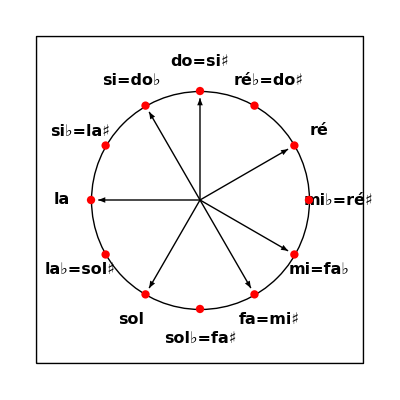

```mathematica
a=4.5;Graphics[{Line[{{-a,-a},{-a,a},{a,a},{a,-a},{-a,-a}}],Circle[{0,0},3],PointSize[0.026],Table[Arrow[{{0,0},{2.8Cos[theta[doremifasollasiChrom[[k]]]],2.8Sin[theta[doremifasollasiChrom[[k]]]]}}],{k,7}],Table[Text[Style[notes12[[k]],Bold,FontSize->16],{3.8Cos[theta[noteschromatiques[[k]]]],3.8Sin[theta[noteschromatiques[[k]]]]}],{k,1,12}],Red,PointSize[0.015],Table[Point[{3Cos[(2k π)/12],3Sin[(2k π)/12]}],{k,0,11}]}]
```

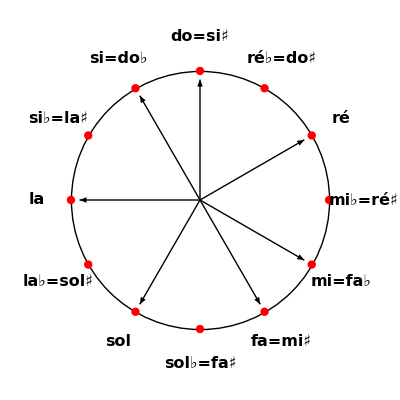

```mathematica
Graphics[{Circle[{0,0},3],PointSize[0.026],Table[Arrow[{{0,0},{2.8Cos[theta[doremifasollasiChrom[[k]]]],2.8Sin[theta[doremifasollasiChrom[[k]]]]}}],{k,7}],Table[Text[Style[notes12[[k]],Bold,FontSize->16],{3.8Cos[theta[noteschromatiques[[k]]]],3.8Sin[theta[noteschromatiques[[k]]]]}],{k,1,12}],Red,PointSize[0.015],Table[Point[{3Cos[(2k π)/12],3Sin[(2k π)/12]}],{k,0,11}]}]
```

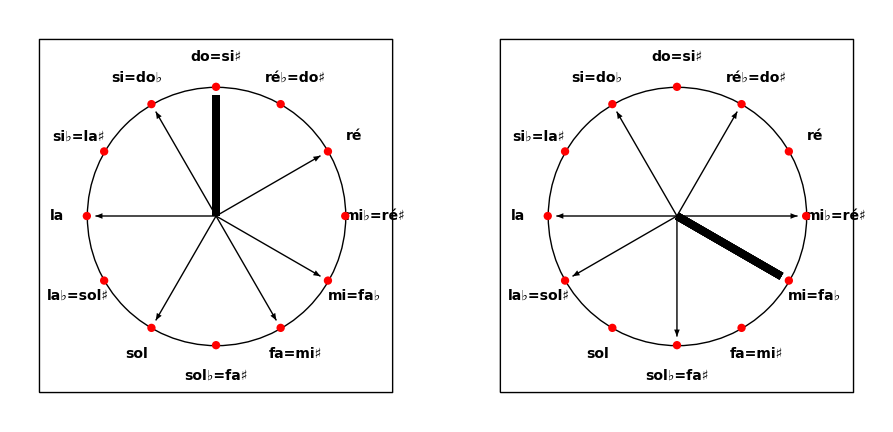

```mathematica
a=4.1;GraphicsGrid[Partition[Table[Graphics[{Line[{{-a,-a},{-a,a},{a,a},{a,-a},{-a,-a}}],Circle[{0,0},3],PointSize[0.026],Rotate[Table[Arrow[{{0,0},{2.8Cos[theta[doremifasollasiChrom[[k]]]],2.8Sin[theta[doremifasollasiChrom[[k]]]]}}],{k,2,7}],-π/600 noteschromatiques[[j]],{0,0}],Thickness[0.014],
Rotate[Table[Arrow[{{0,0},{2.8Cos[theta[doremifasollasiChrom[[1]]]],2.8Sin[theta[doremifasollasiChrom[[1]]]]}}],{k,2,7}],-π/600 noteschromatiques[[j]],{0,0}],Table[Text[Style[notes12[[k]],Bold,FontSize->14],{3.7Cos[theta[noteschromatiques[[k]]]],3.7Sin[theta[noteschromatiques[[k]]]]}],{k,1,12}],Red,PointSize[0.015],Table[Point[{3Cos[(2k π)/12],3Sin[(2k π)/12]}],{k,0,11}]}],{j,{1,5}}],2]]
```

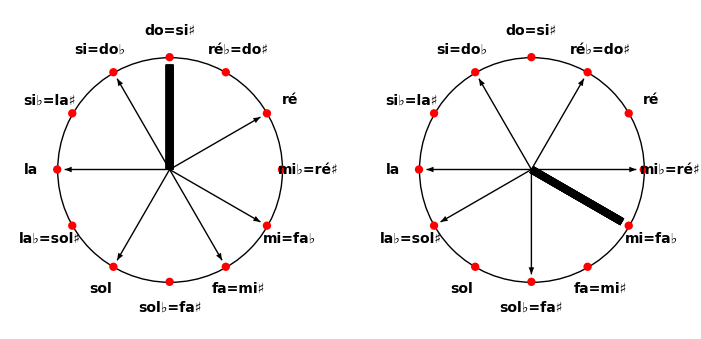

```mathematica
GraphicsGrid[Partition[Table[Graphics[{Circle[{0,0},3],PointSize[0.026],Rotate[Table[Arrow[{{0,0},{2.8Cos[theta[doremifasollasiChrom[[k]]]],2.8Sin[theta[doremifasollasiChrom[[k]]]]}}],{k,2,7}],-π/600 noteschromatiques[[j]],{0,0}],Thickness[0.014],
Rotate[Table[Arrow[{{0,0},{2.8Cos[theta[doremifasollasiChrom[[1]]]],2.8Sin[theta[doremifasollasiChrom[[1]]]]}}],{k,2,7}],-π/600 noteschromatiques[[j]],{0,0}],Table[Text[Style[notes12[[k]],Bold,FontSize->14],{3.7Cos[theta[noteschromatiques[[k]]]],3.7Sin[theta[noteschromatiques[[k]]]]}],{k,1,12}],Red,PointSize[0.015],Table[Point[{3Cos[(2k π)/12],3Sin[(2k π)/12]}],{k,0,11}]}],{j,{1,5}}],2]]
```

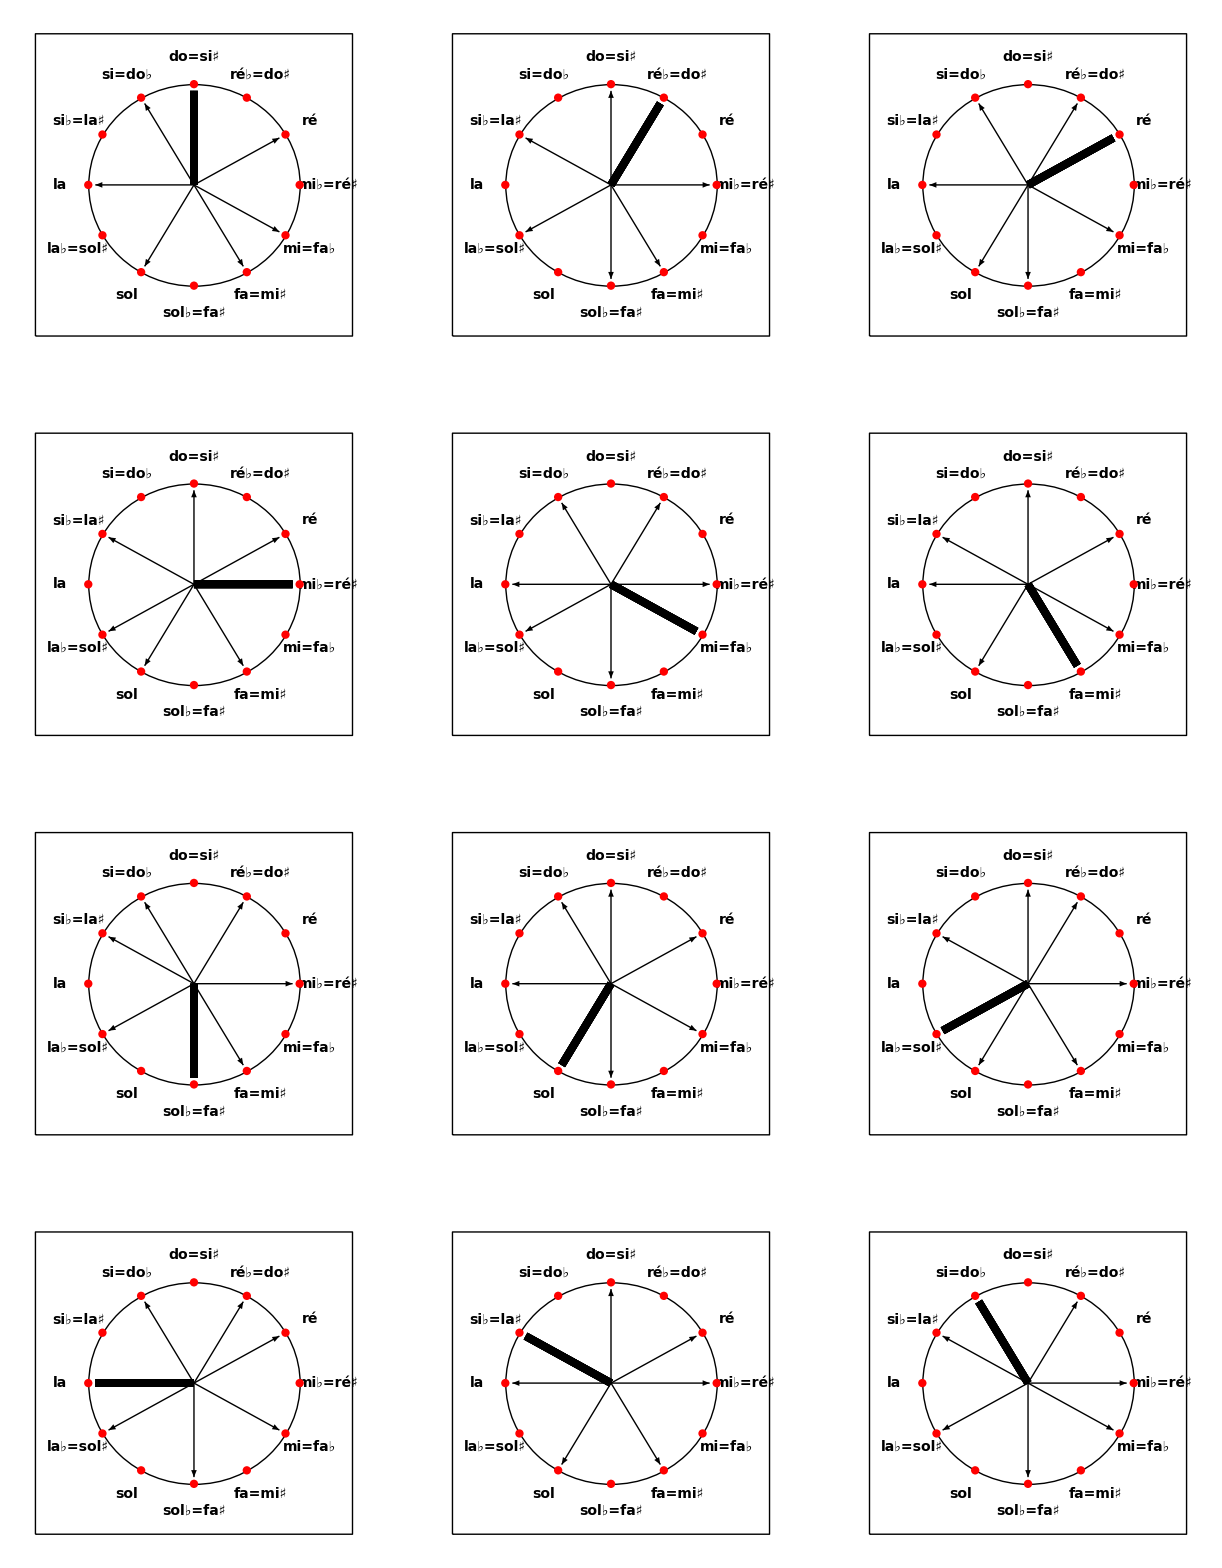

```mathematica
a=4.5;GraphicsGrid[Partition[Table[Graphics[{Line[{{-a,-a},{-a,a},{a,a},{a,-a},{-a,-a}}],Circle[{0,0},3],PointSize[0.026],Rotate[Table[Arrow[{{0,0},{2.8Cos[theta[doremifasollasiChrom[[k]]]],2.8Sin[theta[doremifasollasiChrom[[k]]]]}}],{k,2,7}],-π/600 noteschromatiques[[j]],{0,0}],Thickness[0.014],
Rotate[Table[Arrow[{{0,0},{2.8Cos[theta[doremifasollasiChrom[[1]]]],2.8Sin[theta[doremifasollasiChrom[[1]]]]}}],{k,2,7}],-π/600 noteschromatiques[[j]],{0,0}],Table[Text[Style[notes12[[k]],Bold,FontSize->14],{3.8Cos[theta[noteschromatiques[[k]]]],3.8Sin[theta[noteschromatiques[[k]]]]}],{k,1,12}],Red,PointSize[0.015],Table[Point[{3Cos[(2k π)/12],3Sin[(2k π)/12]}],{k,0,11}]}],{j,1,12}],3]]
```

## Gamme pythagoricienne de William Holder :

```mathematica
{3^12,2^19,N[3^12/2^19]}
```

{531441,524288,1.01364}

```mathematica
{3^53,2^84,N[3^53/2^84]}
```

{19383245667680019896796723,19342813113834066795298816,1.00209}

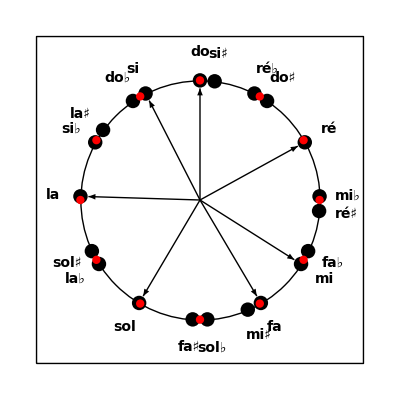

```mathematica
a=4.1;Graphics[{Line[{{-a,-a},{-a,a},{a,a},{a,-a},{-a,-a}}],Circle[{0,0},3],PointSize[0.026],Table[Arrow[{{0,0},{2.8Cos[theta[notesdebase[[k]]]],2.8Sin[theta[notesdebase[[k]]]]}}],{k,7}],Table[Text[Style[notes21[[k]],Bold,FontSize->14],{(3.7+If[k==12,1,0]+If[k==13,1,0])Cos[theta[touteslesnotes21[[k]]]],3.7Sin[theta[touteslesnotes21[[k]]]]}],{k,1,21}],Table[Point[{3Cos[theta[touteslesnotes21[[k]]]],3Sin[theta[touteslesnotes21[[k]]]]}],{k,1,21}],Red,PointSize[0.015],Table[Point[{3Cos[(2k π)/12],3Sin[(2k π)/12]}],{k,0,11}]}]
```

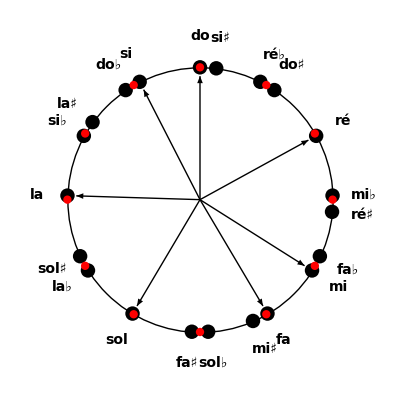

```mathematica
Graphics[{Circle[{0,0},3],PointSize[0.026],Table[Arrow[{{0,0},{2.8Cos[theta[notesdebase[[k]]]],2.8Sin[theta[notesdebase[[k]]]]}}],{k,7}],Table[Text[Style[notes21[[k]],Bold,FontSize->14],{(3.7+If[k==12,1,0]+If[k==13,1,0])Cos[theta[touteslesnotes21[[k]]]],3.7Sin[theta[touteslesnotes21[[k]]]]}],{k,1,21}],Table[Point[{3Cos[theta[touteslesnotes21[[k]]]],3Sin[theta[touteslesnotes21[[k]]]]}],{k,1,21}],Red,PointSize[0.015],Table[Point[{3Cos[(2k π)/12],3Sin[(2k π)/12]}],{k,0,11}]}]
```

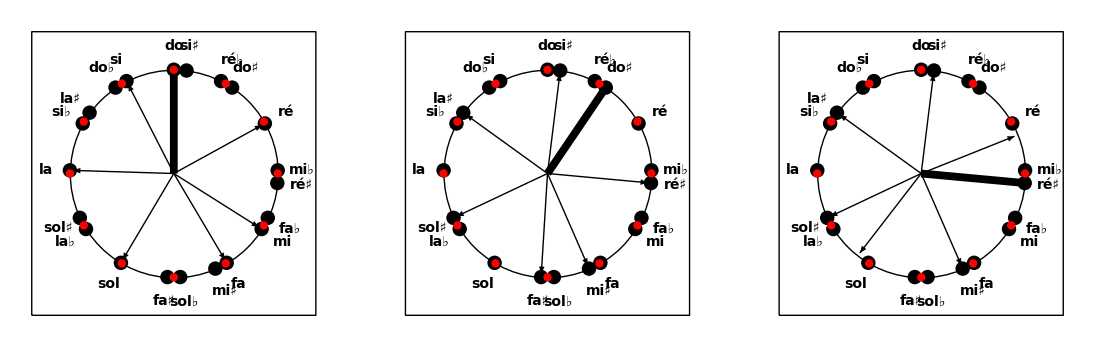

```mathematica
a=4.1;GraphicsGrid[Partition[Table[Graphics[{Line[{{-a,-a},{-a,a},{a,a},{a,-a},{-a,-a}}],Circle[{0,0},3],PointSize[0.026],Rotate[Table[Arrow[{{0,0},{2.9Cos[theta[notesdebase[[k]]]],2.9Sin[theta[notesdebase[[k]]]]}}],{k,2,7}],-π/600 touteslesnotes21[[j]],{0,0}],Thickness[0.014],Rotate[Arrow[{{0,0},{2.9Cos[theta[notesdebase[[1]]]],2.9Sin[theta[notesdebase[[1]]]]}}],-π/600 touteslesnotes21[[j]],{0,0}],Table[Text[Style[notes21[[k]],Bold,FontSize->14],{(3.7+If[k==12,1,0]+If[k==13,1,0])Cos[theta[touteslesnotes21[[k]]]],3.7Sin[theta[touteslesnotes21[[k]]]]}],{k,1,21}],Table[Point[{3Cos[theta[touteslesnotes21[[k]]]],3Sin[theta[touteslesnotes21[[k]]]]}],{k,1,21}],Red,PointSize[0.015],Table[Point[{3Cos[(2k π)/12],3Sin[(2k π)/12]}],{k,0,11}]}],{j,{1,4,7}}],3]]
```

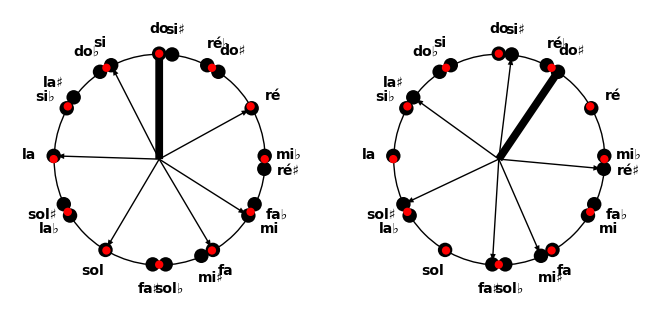

```mathematica
GraphicsGrid[Partition[Table[Graphics[{Circle[{0,0},3],PointSize[0.026],Rotate[Table[Arrow[{{0,0},{2.9Cos[theta[notesdebase[[k]]]],2.9Sin[theta[notesdebase[[k]]]]}}],{k,2,7}],-π/600 touteslesnotes21[[j]],{0,0}],Thickness[0.014],Rotate[Arrow[{{0,0},{2.9Cos[theta[notesdebase[[1]]]],2.9Sin[theta[notesdebase[[1]]]]}}],-π/600 touteslesnotes21[[j]],{0,0}],Table[Text[Style[notes21[[k]],Bold,FontSize->14],{(3.7+If[k==12,1,0]+If[k==13,1,0])Cos[theta[touteslesnotes21[[k]]]],3.7Sin[theta[touteslesnotes21[[k]]]]}],{k,1,21}],Table[Point[{3Cos[theta[touteslesnotes21[[k]]]],3Sin[theta[touteslesnotes21[[k]]]]}],{k,1,21}],Red,PointSize[0.015],Table[Point[{3Cos[(2k π)/12],3Sin[(2k π)/12]}],{k,0,11}]}],{j,{1,4}}],2]]
```

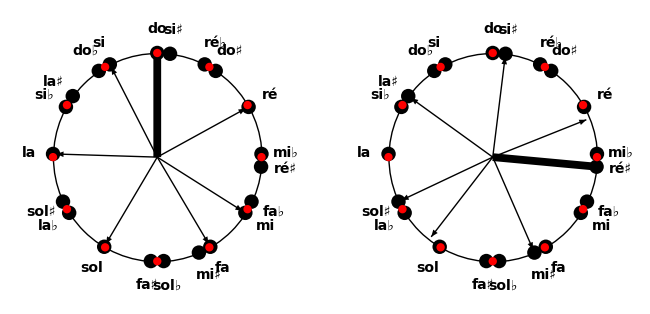

```mathematica
GraphicsGrid[Partition[Table[Graphics[{Circle[{0,0},3],PointSize[0.026],Rotate[Table[Arrow[{{0,0},{2.9Cos[theta[notesdebase[[k]]]],2.9Sin[theta[notesdebase[[k]]]]}}],{k,2,7}],-π/600 touteslesnotes21[[j]],{0,0}],Thickness[0.014],Rotate[Arrow[{{0,0},{2.9Cos[theta[notesdebase[[1]]]],2.9Sin[theta[notesdebase[[1]]]]}}],-π/600 touteslesnotes21[[j]],{0,0}],Table[Text[Style[notes21[[k]],Bold,FontSize->14],{(3.7+If[k==12,1,0]+If[k==13,1,0])Cos[theta[touteslesnotes21[[k]]]],3.7Sin[theta[touteslesnotes21[[k]]]]}],{k,1,21}],Table[Point[{3Cos[theta[touteslesnotes21[[k]]]],3Sin[theta[touteslesnotes21[[k]]]]}],{k,1,21}],Red,PointSize[0.015],Table[Point[{3Cos[(2k π)/12],3Sin[(2k π)/12]}],{k,0,11}]}],{j,{1,7}}],2]]
```

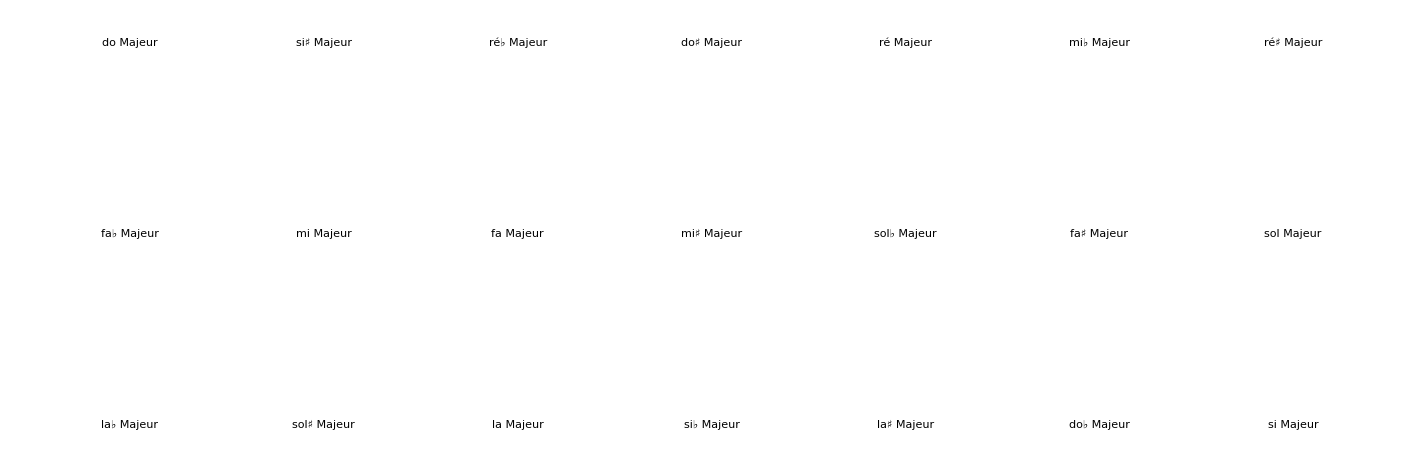

```mathematica
GraphicsGrid[Partition[Table[Labeled[Graphics[{Line[{{-3.5,-3.5},{-3.5,3.5},{3.5,3.5},{3.5,-3.5},{-3.5,-3.5}}],Circle[{0,0},3],PointSize[0.026],Rotate[Table[Arrow[{{0,0},{2.9Cos[theta[notesdebase[[k]]]],2.9Sin[theta[notesdebase[[k]]]]}}],{k,2,7}],-π/600 touteslesnotes21[[j]],{0,0}],Thickness[0.014],Rotate[Arrow[{{0,0},{2.9Cos[theta[notesdebase[[1]]]],2.9Sin[theta[notesdebase[[1]]]]}}],-π/600 touteslesnotes21[[j]],{0,0}],Table[Point[{3Cos[theta[touteslesnotes21[[k]]]],3Sin[theta[touteslesnotes21[[k]]]]}],{k,1,21}],Red,PointSize[0.015],Table[Point[{3Cos[(2k π)/12],3Sin[(2k π)/12]}],{k,0,11}]}],StringJoin[{notes21[[j]]," Majeur"}]],{j,21}],7]]
```

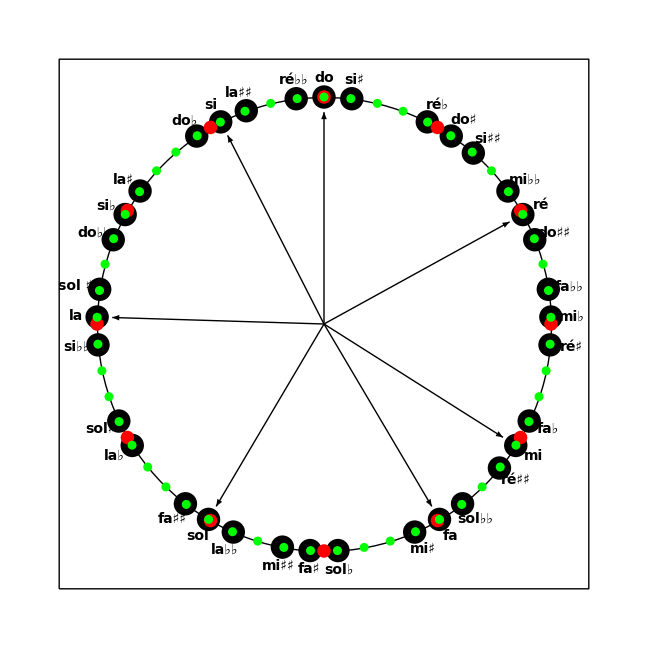

```mathematica
Graphics[{Line[{{-3.5,-3.5},{-3.5,3.5},{3.5,3.5},{3.5,-3.5},{-3.5,-3.5}}],Circle[{0,0},3],PointSize[0.026],Table[Arrow[{{0,0},{2.8Cos[theta[notesdebase[[k]]]],2.8Sin[theta[notesdebase[[k]]]]}}],{k,7}],Table[Text[Style[notes35[[k]],Bold,FontSize->14],{3.28Cos[theta[touteslesnotes35[[k]]]],3.25Sin[theta[touteslesnotes35[[k]]]]}],{k,1,35}],Table[Point[{3Cos[theta[touteslesnotes35[[k]]]],3Sin[theta[touteslesnotes35[[k]]]]}],{k,1,35}],Red,PointSize[0.015],Table[Point[{3Cos[(2k π)/12],3Sin[(2k π)/12]}],{k,0,11}],Green,PointSize[0.010],Table[Point[{3Cos[theta[1200 k/53]],3Sin[theta[1200 k/53]]}],{k,0,52}]}]
```

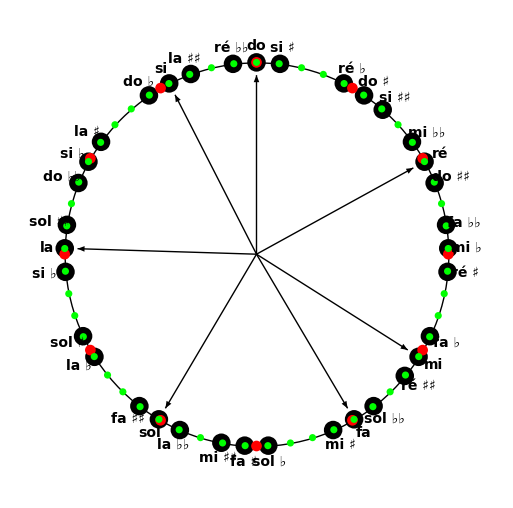

```mathematica
Graphics[{Circle[{0,0},3],PointSize[0.026],Table[Arrow[{{0,0},{2.8Cos[theta[notesdebase[[k]]]],2.8Sin[theta[notesdebase[[k]]]]}}],{k,7}],Table[Text[Style[notes35[[k]],Bold,FontSize->14],{3.28Cos[theta[touteslesnotes35[[k]]]],3.25Sin[theta[touteslesnotes35[[k]]]]}],{k,1,35}],Table[Point[{3Cos[theta[touteslesnotes35[[k]]]],3Sin[theta[touteslesnotes35[[k]]]]}],{k,1,35}],Red,PointSize[0.015],Table[Point[{3Cos[(2k π)/12],3Sin[(2k π)/12]}],{k,0,11}],Green,PointSize[0.010],Table[Point[{3Cos[theta[1200 k/53]],3Sin[theta[1200 k/53]]}],{k,0,52}]}]
```

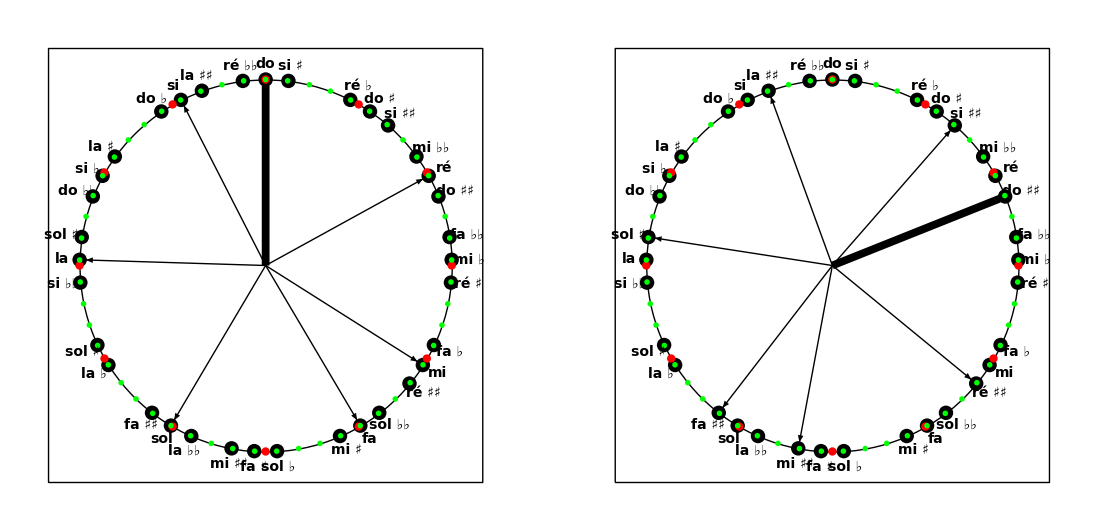

```mathematica
GraphicsGrid[Partition[Table[Graphics[{Line[{{-3.5,-3.5},{-3.5,3.5},{3.5,3.5},{3.5,-3.5},{-3.5,-3.5}}],Circle[{0,0},3],PointSize[0.026],Rotate[Table[Arrow[{{0,0},{2.9Cos[theta[notesdebase[[k]]]],2.9Sin[theta[notesdebase[[k]]]]}}],{k,2,7}],-π/600 touteslesnotes35[[j]],{0,0}],Thickness[0.014],Rotate[Arrow[{{0,0},{2.9Cos[theta[notesdebase[[1]]]],2.9Sin[theta[notesdebase[[1]]]]}}],-π/600 touteslesnotes35[[j]],{0,0}],Table[Text[Style[notes35[[k]],Bold,FontSize->14],{3.28Cos[theta[touteslesnotes35[[k]]]],3.25Sin[theta[touteslesnotes35[[k]]]]}],{k,1,35}],Table[Point[{3Cos[theta[touteslesnotes35[[k]]]],3Sin[theta[touteslesnotes35[[k]]]]}],{k,1,35}],Red,PointSize[0.015],Table[Point[{3Cos[(2k π)/12],3Sin[(2k π)/12]}],{k,0,11}],Green,PointSize[0.010],Table[Point[{3Cos[theta[1200 k/53]],3Sin[theta[1200 k/53]]}],{k,0,52}]}],{j,{1,8}}],2]]
```

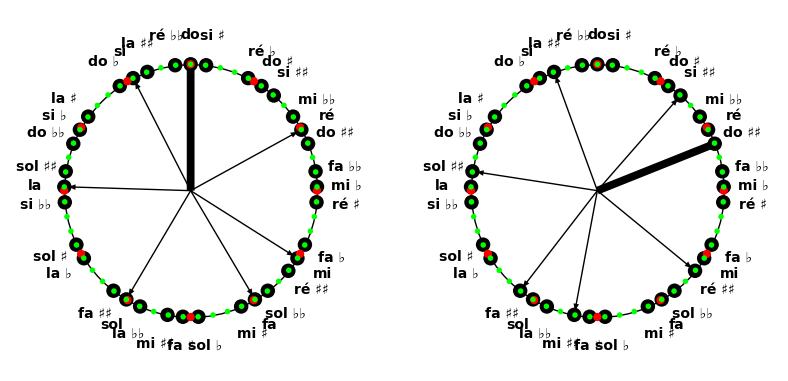

```mathematica
GraphicsGrid[Partition[Table[Graphics[{Circle[{0,0},3],PointSize[0.026],Rotate[Table[Arrow[{{0,0},{2.9Cos[theta[notesdebase[[k]]]],2.9Sin[theta[notesdebase[[k]]]]}}],{k,2,7}],-π/600 touteslesnotes35[[j]],{0,0}],Thickness[0.014],Rotate[Arrow[{{0,0},{2.9Cos[theta[notesdebase[[1]]]],2.9Sin[theta[notesdebase[[1]]]]}}],-π/600 touteslesnotes35[[j]],{0,0}],Table[Text[Style[notes35[[k]],Bold,FontSize->14],{(3.7+If[k==35,1,0]+If[k==1,1,0]+If[k==2,0.5,0]+If[k==18,2,0]+If[k==20,1,0])Cos[theta[touteslesnotes35[[k]]]],3.7Sin[theta[touteslesnotes35[[k]]]]}],{k,1,35}],Table[Point[{3Cos[theta[touteslesnotes35[[k]]]],3Sin[theta[touteslesnotes35[[k]]]]}],{k,1,35}],Red,PointSize[0.015],Table[Point[{3Cos[(2k π)/12],3Sin[(2k π)/12]}],{k,0,11}],Green,PointSize[0.010],Table[Point[{3Cos[theta[1200 k/53]],3Sin[theta[1200 k/53]]}],{k,0,52}]}],{j,{1,8}}],2]]
```

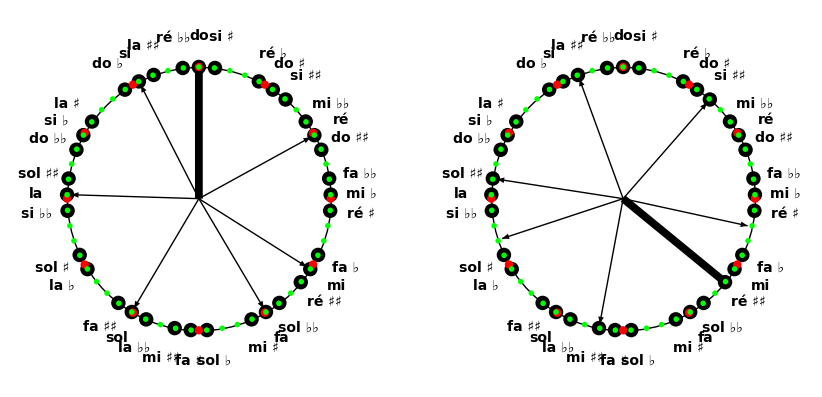

```mathematica
GraphicsGrid[Partition[Table[Graphics[{Circle[{0,0},3],PointSize[0.026],Rotate[Table[Arrow[{{0,0},{2.9Cos[theta[notesdebase[[k]]]],2.9Sin[theta[notesdebase[[k]]]]}}],{k,2,7}],-π/600 touteslesnotes35[[j]],{0,0}],Thickness[0.014],Rotate[Arrow[{{0,0},{2.9Cos[theta[notesdebase[[1]]]],2.9Sin[theta[notesdebase[[1]]]]}}],-π/600 touteslesnotes35[[j]],{0,0}],Table[Text[Style[notes35[[k]],Bold,FontSize->14],{(3.7+If[k==35,1,0]+If[k==1,1,0]+If[k==2,0.5,0]+If[k==18,2,0]+If[k==20,1,0])Cos[theta[touteslesnotes35[[k]]]],3.7Sin[theta[touteslesnotes35[[k]]]]}],{k,1,35}],Table[Point[{3Cos[theta[touteslesnotes35[[k]]]],3Sin[theta[touteslesnotes35[[k]]]]}],{k,1,35}],Red,PointSize[0.015],Table[Point[{3Cos[(2k π)/12],3Sin[(2k π)/12]}],{k,0,11}],Green,PointSize[0.010],Table[Point[{3Cos[theta[1200 k/53]],3Sin[theta[1200 k/53]]}],{k,0,52}]}],{j,{1,14}}],2]]
```

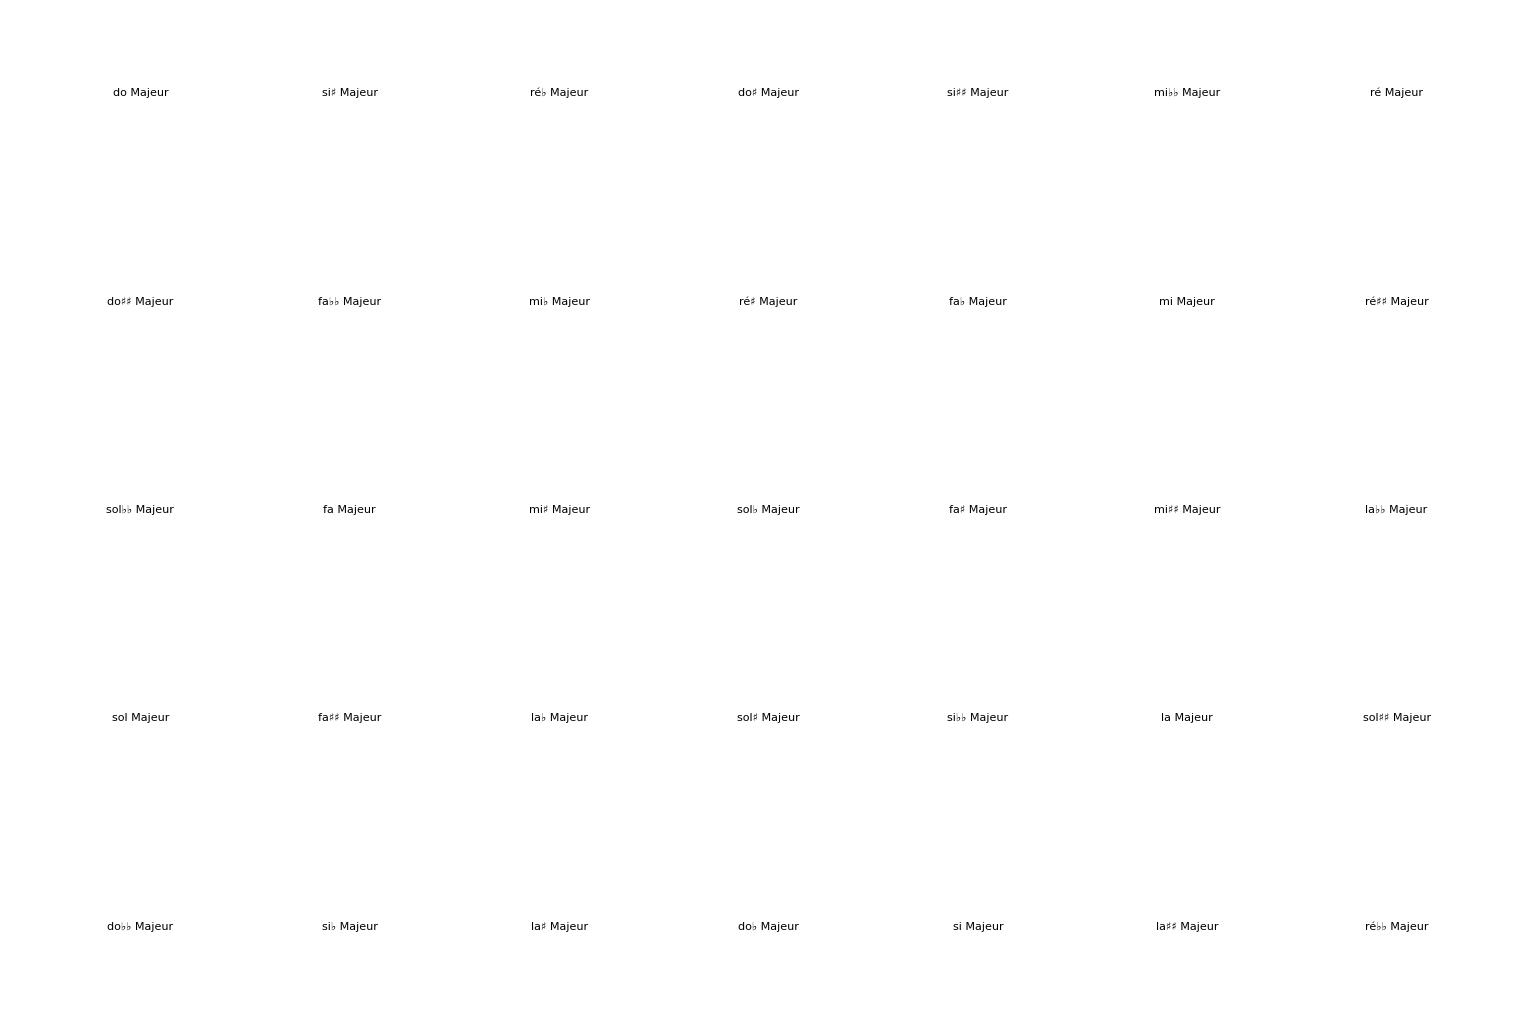

```mathematica
GraphicsGrid[Partition[Table[Labeled[Graphics[{Line[{{-3.5,-3.5},{-3.5,3.5},{3.5,3.5},{3.5,-3.5},{-3.5,-3.5}}],Circle[{0,0},3],PointSize[0.026],Rotate[Table[Arrow[{{0,0},{2.9Cos[theta[notesdebase[[k]]]],2.9Sin[theta[notesdebase[[k]]]]}}],{k,2,7}],-π/600 touteslesnotes35[[j]],{0,0}],Thickness[0.014],Rotate[Arrow[{{0,0},{2.9Cos[theta[notesdebase[[1]]]],2.9Sin[theta[notesdebase[[1]]]]}}],-π/600 touteslesnotes35[[j]],{0,0}],Table[Point[{3Cos[theta[touteslesnotes35[[k]]]],3Sin[theta[touteslesnotes35[[k]]]]}],{k,1,35}],Red,PointSize[0.015],Table[Point[{3Cos[(2k π)/12],3Sin[(2k π)/12]}],{k,0,11}]}],StringJoin[{notes35[[j]]," Majeur"}]],{j,35}],7]]
```

```mathematica
quintesascendantes =Sort[Mod[1200.Log[2,Table[NestWhile[#/2&,2/3(3/2)^k,#≥2&],{k,0,20}]],1200]]
```

{0.,23.46,113.685,137.145,203.91,227.37,317.595,407.82,431.28,498.045,521.505,611.73,635.19,701.955,725.415,815.64,905.865,929.325,1019.55,1109.78,1133.24}

```mathematica
quintesdescendantes =Sort[Mod[1200.Log[2,Table[NestWhile[2# &,2/3(3/2)^k,#<1&],{k,-1,-14,-1}]],1200]]
```

{90.225,180.45,270.675,294.135,384.36,474.585,588.27,678.495,792.18,882.405,972.63,996.09,1086.31,1176.54}

```mathematica
Length[quintesdescendantes ]
```

14

```mathematica
Union[quintesascendantes ,quintesdescendantes ]            (*Identique à touteslesnotes35 *)
```

{0.,23.46,90.225,113.685,137.145,180.45,203.91,227.37,270.675,294.135,317.595,384.36,407.82,431.28,474.585,498.045,521.505,588.27,611.73,635.19,678.495,701.955,725.415,792.18,815.64,882.405,905.865,929.325,972.63,996.09,1019.55,1086.31,1109.78,1133.24,1176.54}

```mathematica
quartesascendantes =Sort[1200.Log[2,Table[NestWhile[#/2&,(4/3)^k,#≥2&],{k,0,18}]]]
```

{0.,66.765,90.225,180.45,270.675,294.135,384.36,474.585,498.045,564.81,588.27,678.495,768.72,792.18,882.405,972.63,996.09,1086.31,1176.54}

```mathematica
Union[quintesascendantes ,quartesascendantes ]
```

{0.,23.46,66.765,90.225,113.685,180.45,203.91,227.37,270.675,294.135,317.595,384.36,407.82,431.28,474.585,498.045,521.505,564.81,588.27,611.73,635.19,678.495,701.955,725.415,768.72,792.18,815.64,882.405,905.865,929.325,972.63,996.09,1019.55,1086.31,1109.78,1133.24,1176.54}

```mathematica
Sort[Table[NestWhile[#/2&,(3/2)^k,#≥2&],{k,0,11}]]//N                 (*A comparer au schéma exactement tempéré*)
```

{1.,1.06787,1.125,1.20135,1.26563,1.35152,1.42383,1.5,1.60181,1.6875,1.80203,1.89844}

```mathematica
Sort[Table[NestWhile[#/2&,(3/2)^k,#≥2&],{k,0,12}]]//N                  (*Observer que le cycle ne se referme pas exactement : on dépasse 2, d'où la présence de 1.01364*)
```

{1.,1.01364,1.06787,1.125,1.20135,1.26563,1.35152,1.42383,1.5,1.60181,1.6875,1.80203,1.89844}

```mathematica
Ratios[Sort[Table[NestWhile[#/2&,(3/2)^k,#≥2&],{k,0,11}]]]          (*On ne trouve que deux intervalles : tc=1200Log[2,2187/2048]=90.225 et td=1200Log[2,256/243]=113.685*)
```

{2187/2048,256/243,2187/2048,256/243,2187/2048,256/243,256/243,2187/2048,256/243,2187/2048,256/243}

```mathematica
Ratios[Sort[Table[NestWhile[#/2&,(4/3)^k,#≥2&],{k,0,12}]]]
```

{256/243,256/243,2187/2048,256/243,2187/2048,256/243,256/243,2187/2048,256/243,2187/2048,256/243,256/243}

```mathematica
Table[(3/2)^k,{k,0,12}]
```

{1,3/2,9/4,27/8,81/16,243/32,729/64,2187/128,6561/256,19683/512,59049/1024,177147/2048,531441/4096}

## Partition simplifiée

```mathematica
Length[%]
```

42

## Schéma de quintes ascendantes :

```mathematica
Table[(3/2)^k,{k,0,11}]//N
```

{1.,1.5,2.25,3.375,5.0625,7.59375,11.3906,17.0859,25.6289,38.4434,57.665,86.4976}

## Quintes ascendantes ramenées à une octave unique et triées :

```mathematica
Sort[Table[NestWhile[#/2&,(3/2)^k,#≥2&],{k,0,11}]]
```

{1,531441/524288,2187/2048,9/8,19683/16384,81/64,177147/131072,729/512,3/2,6561/4096,27/16,59049/32768,243/128}

```mathematica
Sort[Table[NestWhile[#/2&,(3/2)^k,#≥2&],{k,0,12}]]//N
```

{1.,1.01364,1.06787,1.125,1.20135,1.26563,1.35152,1.42383,1.5,1.60181,1.6875,1.80203,1.89844}

```mathematica
Ratios[{1.,1.0136432647705078,1.06787109375,1.125,1.20135498046875,1.265625,1.3515243530273438,1.423828125,1.5,1.601806640625,1.6875,1.802032470703125,1.8984375,2}]
```

{1.01364,1.0535,1.0535,1.06787,1.0535,1.06787,1.0535,1.0535,1.06787,1.0535,1.06787,1.0535,1.0535}

```mathematica
Ratios[{1,2187/2048,9/8,19683/16384,81/64,177147/131072,729/512,3/2,6561/4096,27/16,59049/32768,243/128,2}]
```

{2187/2048,256/243,2187/2048,256/243,2187/2048,256/243,256/243,2187/2048,256/243,2187/2048,256/243,256/243}

```mathematica
Table[NestWhile[#/2&,(3/2)^k,#≥2&],{k,0,11}]
```

{1,3/2,9/8,27/16,81/64,243/128,729/512,2187/2048,6561/4096,19683/16384,59049/32768,177147/131072}

```mathematica
Table[NestWhile[#/2&,(3/2)^k,#≥2&],{k,0,12}]//N
```

{1.,1.5,1.125,1.6875,1.26563,1.89844,1.42383,1.06787,1.60181,1.20135,1.80203,1.35152,1.01364}

```mathematica
Ratios[Sort[Table[NestWhile[#/2&,(3/2)^k,#≥2&],{k,0,35}]]]
```

{531441/524288,531441/524288,134217728/129140163,531441/524288,531441/524288,70368744177664/68630377364883,531441/524288,531441/524288,134217728/129140163,531441/524288,531441/524288,70368744177664/68630377364883,531441/524288,531441/524288,134217728/129140163,531441/524288,531441/524288,70368744177664/68630377364883,531441/524288,531441/524288,70368744177664/68630377364883,531441/524288,531441/524288,134217728/129140163,531441/524288,531441/524288,70368744177664/68630377364883,531441/524288,531441/524288,134217728/129140163,531441/524288,531441/524288,70368744177664/68630377364883,531441/524288,531441/524288}

```mathematica
{1200Log[2,531441/524288],1200Log[2,134217728/129140163],1200Log[2,70368744177664/68630377364883]}//N
```

{23.46,66.765,43.305}

```mathematica
3{23.460010384649014,66.7649852884139,43.304974903764894}/Total[{23.460010384649014,66.7649852884139,43.304974903764894}]
```

{0.527073,1.5,0.972927}

```mathematica
{1200Log[2,2187/2048],1200Log[2,256/243]}//N
```

{113.685,90.225}

```mathematica
113.68500605771193/90.22499567306305
```

1.26002

```mathematica
1200Log[2,#]&/@Ratios[Sort[Table[NestWhile[#/2&,(3/2)^k,#≥2&],{k,0,12}]]]//N            (*Observer que le cycle ne se referme pas exactement : on dépasse 2*)
```

{23.46,90.225,90.225,113.685,90.225,113.685,90.225,90.225,113.685,90.225,113.685,90.225}

```mathematica
Total[{23.460010384649014,90.22499567306305,90.22499567306305,113.68500605771193,90.22499567306305,113.68500605771193,90.22499567306305,90.22499567306305,113.68500605771193,90.22499567306305,113.68500605771193,90.22499567306305}]
```

1109.78

## Schéma de quintes descendantes :

```mathematica
Table[(3/2)^k,{k,0,-11,-1}]//N
```

{1.,0.666667,0.444444,0.296296,0.197531,0.131687,0.0877915,0.0585277,0.0390184,0.0260123,0.0173415,0.011561}

## Quintes descendantes ramenées à une octave unique :

```mathematica
Sort[Table[NestWhile[2# &,2(3/2)^k,#<1&],{k,0,-11,-1}]]
```

{256/243,65536/59049,32/27,8192/6561,4/3,1024/729,262144/177147,128/81,32768/19683,16/9,4096/2187,2}

```mathematica
Ratios[Sort[Table[NestWhile[2# &,2(3/2)^k,#<1&],{k,0,-11,-1}]]]
```

{256/243,2187/2048,256/243,2187/2048,256/243,256/243,2187/2048,256/243,2187/2048,256/243,2187/2048}

```mathematica
{2187/2048,256/243,2187/2048,256/243,2187/2048,256/243,256/243,2187/2048,256/243,2187/2048,256/243}
```

## En résumé :

```mathematica
{tc,td,tc+ td,tc- td,2td-tc}//N
```

{113.685,90.225,203.91,23.46,66.765}

```mathematica
5tc+7td//Simplify
```

1200

```mathematica
intervMAJencents={0,tc +td,tc +td, td,tc +td,tc +td,tc+ td,td};
```

```mathematica
Accumulate[intervMAJencents]//N
```

{0.,203.91,407.82,498.045,701.955,905.865,1109.78,1200.}

```mathematica
notesdebase=Most[Accumulate[intervMAJencents]]//N
```

{0.,203.91,407.82,498.045,701.955,905.865,1109.78}

```mathematica
touteslesnotes=Sort[Join[notesdebase,Mod[notesdebase+tc,1200.],Mod[notesdebase-tc,1200.]]]
```

{0.,23.46,90.225,113.685,203.91,294.135,317.595,384.36,407.82,498.045,521.505,588.27,611.73,701.955,792.18,815.64,905.865,996.09,1019.55,1086.31,1109.78}

```mathematica
Length[touteslesnotes]
```

21

```mathematica
Append[Differences[touteslesnotes],90.22499567306306]
```

{23.46,66.765,23.46,90.225,90.225,23.46,66.765,23.46,90.225,23.46,66.765,23.46,90.225,90.225,23.46,90.225,90.225,23.46,66.765,23.46,90.225}

```mathematica
theta[t_]:=Mod[(300-t)/300 π/2,2π]
```

```mathematica
s[q_]:=Mod[300-600 q/π,1200]
```

```mathematica
theta[t_]:=Mod[(300-t)/300 π/2,2π]
```

```mathematica
s[theta[1.1]]
```

1.1

```mathematica
theta[905.87]
```

3.11086

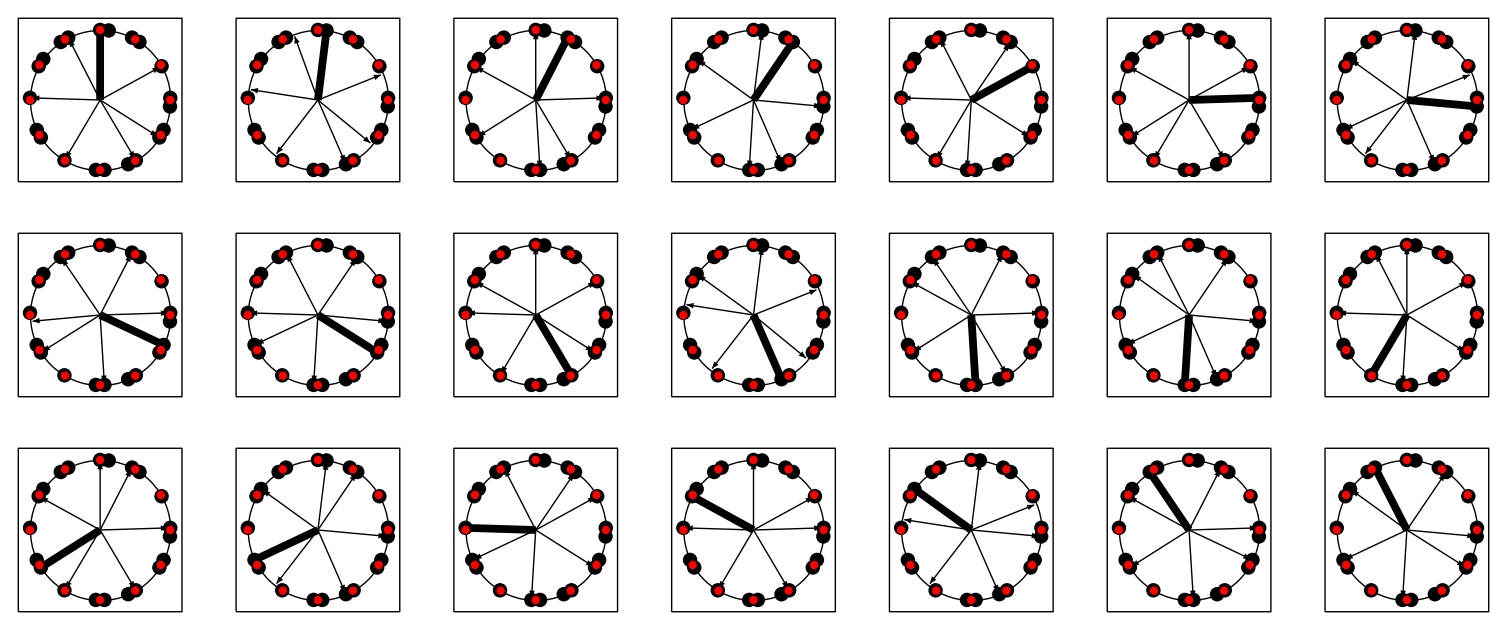

```mathematica
GraphicsGrid[Partition[Table[Graphics[{Line[{{-3.5,-3.5},{-3.5,3.5},{3.5,3.5},{3.5,-3.5},{-3.5,-3.5}}],Circle[{0,0},3],PointSize[0.026],Rotate[Table[Arrow[{{0,0},{2.9Cos[theta[notesdebase[[k]]]],2.9Sin[theta[notesdebase[[k]]]]}}],{k,2,7}],-π/600 touteslesnotes[[k]],{0,0}],Thickness[0.014],Rotate[Arrow[{{0,0},{2.9Cos[theta[notesdebase[[1]]]],2.9Sin[theta[notesdebase[[1]]]]}}],-π/600 touteslesnotes[[k]],{0,0}],Table[Point[{3Cos[theta[touteslesnotes[[k]]]],3Sin[theta[touteslesnotes[[k]]]]}],{k,1,21}],Red,PointSize[0.015],Table[Point[{3Cos[(2k π)/12],3Sin[(2k π)/12]}],{k,0,11}]}],{k,21}],7]]
```